```mathematica
sol=NDSolve[{v'[t]==x[t]-x[t]^3-0.05*v[t]+0.1 Cos[1.1*t],x'[t]==v[t],x[0]==0,v[0]==0},{x,v},{t,0,200},MaxSteps->3500];
```

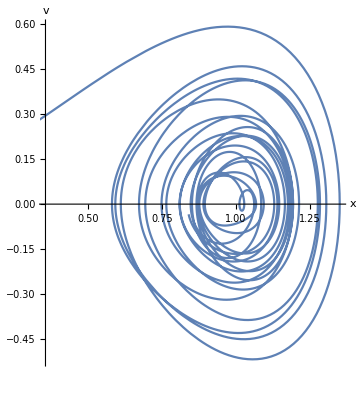

```mathematica
ParametricPlot[{x[t],v[t]}/. sol,{t,0,100},AxesLabel->{"x","v"}]
```

```mathematica
Clear[A];
solution[A_,tmax_]:=NDSolve[{v'[t]==x[t]-x[t]^3-0.05*v[t]+A*Cos[1.1*t],x'[t]==v[t],x[0]==0,v[0]==0},{x,v},{t,0,tmax},MaxSteps->100*tmax]
```

```mathematica
sol3=solution[0.2,800]
```

{{x→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

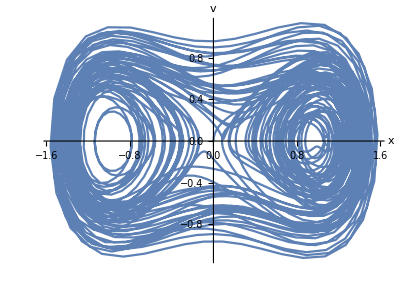

```mathematica
graph[tmin_,tmax_]:=ParametricPlot[Evaluate[{x[t],v[t]}/. sol3],{t,tmin,tmax},AxesLabel->{"x","v"}]
graph[0,600]
```

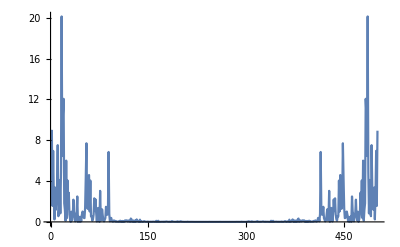

```mathematica
ListLinePlot[Abs[Fourier[Flatten[Table[Evaluate[x[t]/.sol3], {t,100,600}]]]]^2,PlotRange->All]
```

```mathematica
motion = NDSolve[{x''[t]+1/10 x'[t]+x[t]+x[t]^3== Sin[5 t]+Sin[7 t],
x[0]==0, x'[0]==0}, x[t], {t,80,180}][[1]]
```

{x[t]→InterpolatingFunction[…][t]}

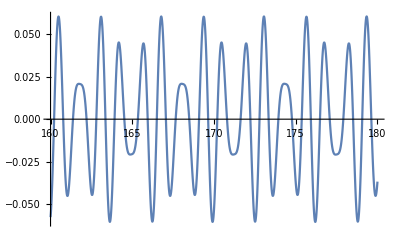

```mathematica
Plot[x[t]/.motion, {t,160,180}, Ticks->False]
```

```mathematica
discretizedmotion = Table[x[t]/.motion, {t,80,180,.05}];
```

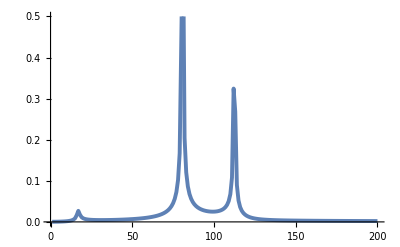

```mathematica
powerspectrum = ListPlot[Take[Abs[Fourier[discretizedmotion]],{1,200}], Joined->True,PlotRange->{0.,0.5}, PlotStyle->Thickness[0.007], Ticks->False]
```